# PrecessingTemplate-ExplainTestScript-Lundgren

Goal: Report on test script

spintaylor_t2_f2_faithfulness
Reproduces Fig 1 in the text.  Can be used to identify precisely when our approximation breaks down

```mathematica
SetDirectory[NotebookDirectory[]]
```

#### Plot of results

These plots use data generated by spintaylor_t2_f2_faithfulness

```mathematica
tmp1 = Import["fiducial_results.dat", "Table"];
tmp1[[1]]
tmp1 = Drop[tmp1,1];
```

{{#,mass1,mass2,inclination,chi1x,chi1y,chi1z,psi,phi0,chi,kappa,faithfulness},{10.,1.4,2.13528,-0.236361,0.143596,-0.470915,1.36914,2.42704,0.5461,0.0956,0.9983},«40048»,{10.,1.4,1.0578,0.448857,-0.165212,0.637457,3.62941,4.841,0.7969,0.8833,0.9985}}

Cumulative match distribution : Figure 1 in the paper

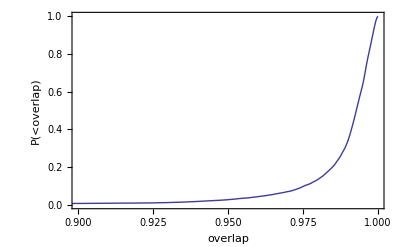

0.135648

0.0277908

0.00794971

```mathematica
distrib = SmoothKernelDistribution[tmp1[[All,-1]], 0.0001];
pNet = Plot[CDF[distrib][x], {x,0,1}, PlotRange->{{0.9,1},{0,1}}, Frame->True,Axes->False,FrameLabel->{"overlap", "P(<overlap)"}]
CDF[distrib][0.98] (* fraction with matches lower than 0.98 *)
CDF[distrib][0.95] (* fraction with matches lower than 0.95 *)
CDF[distrib][0.90] (* fraction with matches lower than 0.90 *)
```

```mathematica
Export[$HomeDirectory<>"/fig-mma-FaithfulnessCumulative-New.pdf", pNet, "PDF"]
```

/Users/oshaughn/fig-mma-FaithfulnessCumulative-New.pdf

Where does the approximation break down?: The approximation breaks down for some (but not all!) rapidly spinning binaries with misaligned spins.

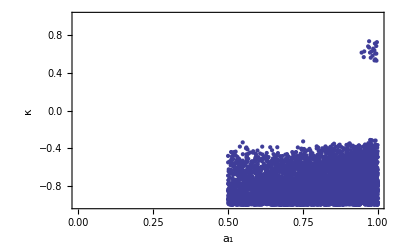

```mathematica
ListPlot[(chi = Take[#, {4,6}]; {Sqrt[ chi.chi], #[[-2]]})&/@Select[tmp1, (#[[-1]]<0.98)&], PlotRange->{{0,1}, {-1,1}},Frame->True, Axes->False, FrameLabel->{"a_1", "κ",  "Where low overlaps come from"}]
```

```mathematica
ListPointPlot3D[(chi = Take[#, {4,6}]; {Sqrt[ chi.chi], #[[-2]], #[[-1]]})&/@ tmp1, PlotRange->{0.8,1}]
```

-Graphics3D-